#### Hilbert Space (example state: E_1 G_10 represented as {3, 1, 0} )

```mathematica
NumberOfAtoms=2; (* only two -- locked choice for now *)
NumberOfSubspaces = 2; (* G1 or G2 --- only two -- locked choice for now *)
NumberOfModes = 1;
ExcitedLevel[Subspace_]=NumberOfSubspaces+Subspace;

cons[Atom_,Subspace_,Type_]:=
Module[{a},
a=ConstantArray[KroneckerDelta[Subspace,1](1+Type,2)+KroneckerDelta[Subspace,2](1+Type,1),NumberOfAtoms+NumberOfModes];
a[[Atom]]=ExcitedLevel[Subspace];
a[[NumberOfAtoms+1;;]]=0;
a ];

For[m=1,m<=NumberOfAtoms,m++,

(* Subspace I *)
ψI[m]= cons[m,1,1];

(* Subspace II *)
ψII[m]= cons[m,1,2];

(* Subspace III *)
ψIII[m]= cons[m,2,1];

(* Subspace IV *)
ψIV[m]= cons[m,2,2];
];

ClearAll[m];

InitialStates=(ψI[#]&/@Range[NumberOfAtoms])~Join~(ψII[#]&/@Range[NumberOfAtoms])~Join~(ψIII[#]&/@Range[NumberOfAtoms])~Join~(ψIV[#]&/@Range[NumberOfAtoms]);
Boundary= InitialStates;
Known = InitialStates;

NextStates[KnownStates_,BoundaryStates_]:=
Module[
{a,b,NextKnown,NextBoundary},
b={};
Do[(* Go through all the boundary states *)

Do[(* Check the states of all the atoms one by one *)

(* Subscript[E, 1] can change to Subscript[G, 1] -- emitting a photon *)
a =BoundaryStates[[m]];
If[
a[[k]]==ExcitedLevel[1],
a[[k]]=1;  
a[[NumberOfAtoms+1]]= a[[NumberOfAtoms+1]]+1;
b=Append[b,a];
];

(* Subscript[E, 2] can change to Subscript[G, 1]  -- no photons emitted yet *)
a =BoundaryStates[[m]];
If[
a[[k]]==ExcitedLevel[2],
a[[k]]=1;  ;
b=Append[b,a];
];

(* Subscript[G, 1] can change to Subscript[E, 2] -- classical light absorbed *)
a =BoundaryStates[[m]];
If[a[[k]]==1,
a[[k]]=ExcitedLevel[2];
b=Append[b,a]];

(* Subscript[G, 1] can change to Subscript[E, 1]-- absorbing a *)
If[a[[k]] =1&&a[[NumberOfAtoms+1]]>0,
a[[k]]=ExcitedLevel[1];  
a[[NumberOfAtoms+1]]= a[[NumberOfAtoms+1]]-1;
b=Append[b,a];
]

,{k,1,NumberOfAtoms}];

,{m,1,Dimensions[BoundaryStates][[1]]}];

b= DeleteDuplicates[b]; (* These are the all the possible next boundary states if they are not already known *)

NextKnown =KnownStates~Join~b;
NextKnown = DeleteDuplicates[NextKnown];

If[Dimensions[NextKnown][[1]]>Dimensions[KnownStates][[1]],
NextBoundary = NextKnown[[Dimensions[KnownStates][[1]]+1;;]]
,NextBoundary={}
];
{NextKnown,NextBoundary}

];

TransitionOrder=0;
For[{tmpk,tmpb} ={ InitialStates, InitialStates},Boundary!={},{Known,Boundary}={tmpk,tmpb},
TransitionOrder=TransitionOrder+1;
{tmpk, tmpb}= NextStates[Known,Boundary];
(*Print[TransitionOrder];
Print[MatrixForm[tmpb]];*)
];
{Known, Boundary}= NextStates[Known, Boundary];
TransitionOrder=TransitionOrder-1;
dimK= Dimensions[Known][[1]];
```

#### Hamiltonian

```mathematica
g1[1]=g1[2]=ωg1;
g2[1]=g2[2]=ωg2;
e1[1]=e1[2]=ωe1;
e2[1]=e2[2]=ωe2;
ℏ=1;
Ωal[1]=Ωal[2]=Ω;


HfieldMatrixElements[p_,q_] := p,q( ℏ ωph  (Known[[p,NumberOfAtoms+1]]));

Hfield = Table[HfieldMatrixElements[p,q],{p,1,dimK},{q,1,dimK}];

HatomsMatrixElements[p_,q_]:=Module[{a},
a=0;
Do[
a = a+p,q(ℏ Known[[p,m]],1 g1[m]+ℏ Known[[p,m]],2 g2[m]+ℏ Known[[p,m]],3 e1[m]+ℏ Known[[p,m]],4 e2[m])  ;
,{m,1,NumberOfAtoms}];
a
];

Hatoms = Table[HatomsMatrixElements[p,q],{p,1,dimK},{q,1,dimK}];

IsEdge[ψ1_,ψ2_]:=Module[{photonEmAbs,diffNum,a},

diffNum=0;
photonEmAbs=0;
a=True;

For[k=1,k<=NumberOfAtoms,k++,

If[ψ1[[k]]!=ψ2[[k]],
diffNum = diffNum +1
];

If[(ψ1[[k]]==3&&ψ2[[k]]==4)∨(ψ1[[k]]==4&&ψ2[[k]]==3),
a=False;
];

If[(ψ1[[k]]==1&&ψ2[[k]]==2)∨(ψ1[[k]]==2&&ψ2[[k]]==1),
a=False;
];

If[(ψ1[[k]]==1&&ψ2[[k]]==3)∨(ψ1[[k]]==3&&ψ2[[k]]==1),
photonEmAbs= photonEmAbs+Sign[ψ1[[k]]-ψ2[[k]]] +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[ψ1[[k]]==3&&ψ2[[k]]==1,
photonEmAbs= photonEmAbs+1 +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[(ψ1[[k]]==1&&ψ2[[k]]==4)∨(ψ1[[k]]==4&&ψ2[[k]]==1),
photonEmAbs= photonEmAbs+0 +ψ1[[NumberOfAtoms+1]]-ψ2[[NumberOfAtoms+1]];
];

If[(ψ1[[k]]==2&&ψ2[[k]]!=2)∨(ψ2[[k]]==2&&ψ1[[k]]!=2),
a=False
];


];
 
a&&(diffNum==1)&&(photonEmAbs==0)

];
```

```mathematica
HintMatrixElements[p_,q_]:=Module[{a},
a=0;
If[IsEdge[Known[[p]],Known[[q]]],

Do[
a= a
+Abs[Known[[p,m]]  - Known[[q,m]]],NumberOfSubspaces ℏ Ωal[m]/2 
+Abs[Known[[p,m]]  - Known[[q,m]]],NumberOfSubspaces+1 ℏ  A  ⅇ^(-Sign[Known[[p,m]]  - Known[[q,m]]]ⅈ υ t)(*2 Cos[υ t]*)

,{m,1,NumberOfAtoms}];
] ;
a
];

Hint = Table[HintMatrixElements[p,q],{p,1,Dimensions[Known][[1]]},{q,1,Dimensions[Known][[1]]}];

H0= Hfield+Hatoms;
Hint = MatrixExp[ⅈ IntPic,1(t/ℏ)H0].Hint.MatrixExp[-ⅈ  IntPic,1(t/ℏ)H0];
Htot=IntPic,0( H0) + Hint;

ωk[ψ_]:=Module[{a},
a=0;
Do[
a=a+Piecewise[{{g1[m], ψ[[m]]==1}, {g2[m], ψ[[m]]==2}, {e1[m], ψ[[m]]==3}, {e2[m], ψ[[m]]==4}}]

,{m,1,NumberOfAtoms}];

ωph ψ[[NumberOfAtoms+1]]+a
];

ωfi[ψf_,ψi_]:=ωk[ψf]-ωk[ψi];

ωe1=ωg1+ωph+Δ;
ωe2=ωg1+Δ+υ;
IntPic=1;
```

#### Graph Plot of the Hilbert space

```mathematica
StateLabel[ψ_]:=Module[{a},
a={};
For [k=1,k<=NumberOfAtoms,k++,
a=Append[a,Piecewise[{{"G_1 ", ψ[[k]]==1}, {"G_2 ", ψ[[k]]==2}, {"E_1 ", ψ[[k]]==3}, {"E_2 ", ψ[[k]]==4}}]]
];
a=Append[a,ψ[[NumberOfAtoms+1]]];
Row@a
];
```

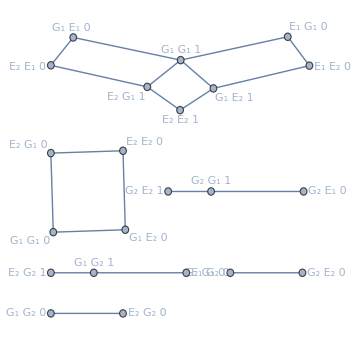

```mathematica
elength={};
FormGraph=Module[{graph},
graph={};
Do[
Do[
If[IsEdge[Known[[i]],Known[[f]]],
AppendTo[graph,i<->f];
AppendTo[elength,If[Known[[i,NumberOfAtoms+1]]==Known[[f,NumberOfAtoms+1]],1,2]
]
]
,{f,i+1,dimK}];
,{i,1,dimK}];
graph
];

graph=Graph[FormGraph,VertexLabels->Table[i->StateLabel[Known[[i]]],{i,1,dimK}],(*GraphLayout->"SpringEmbedding",*)VertexLabelStyle->Medium,VertexSize->Medium,ImageSize->Medium,EdgeWeight->elength,GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}}]
```

(1<->9
1<->10
2<->9
2<->11
3<->12
4<->13
5<->14
6<->15
7<->16
7<->17
8<->16
8<->17
9<->18
9<->19
10<->19
11<->18
12<->20
13<->21
18<->22
19<->22)

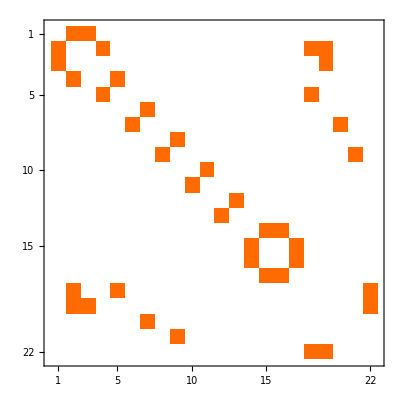

```mathematica
MatrixForm[FormGraph]
MatrixPlot[AdjacencyMatrix[FormGraph]]
```

#### Initial State

```mathematica
X0=ConstantArray[0,dimK];
choice =1;
list=Piecewise[{{{1,1,0,0,0,0,-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}, choice==1(* Heralding on Not Subscript[G, 2] *)}, {{0,0,1,1,ⅇ^(ⅈ ϕ),ⅇ^(ⅈ ϕ),0,0}, choice==2 (* Heralding on Not Subscript[G, 1] *)}, {{1,1,1,1,ⅇ^(ⅈ ϕ),ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}, choice==3 (* Without heralding *)}}]
X0[[1;;8]]=list;
X0=X0/Norm[X0];
```

{1,1,0,0,0,0,-ⅇ^(ⅈ ϕ),-ⅇ^(ⅈ ϕ)}

#### Parameters

```mathematica
t0=0; (* This is after the Zeno measurements *)
tf=0.5 ;
ωg1=0;
ωph=110;
Δ=10;
ωe1=ωg1+ωph+Δ;
υ=100;
ωe2=ωg1+Δ+υ;
ωg2=0;
IntPic=1;
Ω=1  ;
A= 1;
ϕ=0; (* starting phase @ Subscript[t, r] = 0 *)

stepsize=6;
```

#### Schrodinger Equation and Electric Field Matrix

```mathematica
sol=NDSolveValue[{Xsol'[t]==((-ⅈ)/ℏ) Htot.Xsol[t],Xsol[0]==X0},Xsol,{t,0,tf},MaxStepSize->10^-stepsize];

(* Converting a vector valued 'Interpolating Function' Mathematica object to a vector of scalar valued 'Interpolating function' Mathematica objects *)
IFvectorTovectorIF[IFvector_]:=Module[{vectorIF=ConstantArray[0,IFvector["OutputDimensions"][[1]]]},
For[k=1,k<=IFvector["OutputDimensions"][[1]],k++,
vectorIF[[k]]=Transpose[Append[IFvector["Coordinates"],IFvector["ValuesOnGrid"][[All,k]]]];
vectorIF[[k]]=Interpolation[vectorIF[[k]],InterpolationOrder->IFvector["InterpolationOrder"][[1]],Method->IFvector["InterpolationMethod"]][t]
];
vectorIF
];
Xsol[t_]=(* MatrixExp[-ⅈ  IntPic(t /ℏ)H0].*)IFvectorTovectorIF[sol];
Ψ[t_]:=Xsol[t]/Norm[Xsol[t]](ⅇ^(-ⅈ t/ℏ ωk[Known[[#]]])&/@Range[dimK]);

(*Xsol[t_]=(ⅇ^(-ⅈ t/ℏ ωk[Known[[#]]])&/@Range[dimK])sol;*)
Φ[k_] :=Known[[k]];

ElectricFieldMatrixElements[p_,q_]:=Module[{ϕ1,ϕ2,a},
ϕ1=Known[[p]];
ϕ2=Known[[q]];
a=0;
If[ϕ1[[1;;NumberOfAtoms]]==ϕ2[[1;;NumberOfAtoms]],
a=Abs[ϕ1[[NumberOfAtoms+1]]-ϕ2[[NumberOfAtoms+1]]] 
];
a];

ElectricFieldMatrix = Table[ElectricFieldMatrixElements[p,q],{p,1,dimK},{q,1,dimK}];
```

```mathematica
ElectricFieldMatrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
vec=ElectricFieldMatrix.Range[dimK];
```

```mathematica
Do[
If[vec[[k]]!=0,
a=vec[[k]];
(*Print[{Known[[k]],Known[[vec[[k]]]]}];*)
Print[StateLabel[Known[[k]]]];
Print[StateLabel[Known[[a]]]];
Print["----------"];
]
,{k,1,dimK}]
ClearAll[a,vec];
```

E_2 G_2 0

E_2 G_2 1

----------

G_2 E_2 0

G_2 E_2 1

----------

E_2 G_1 0

E_2 G_1 1

----------

G_1 E_2 0

G_1 E_2 1

----------

G_1 G_1 1

G_1 G_1 0

----------

G_1 G_2 1

G_1 G_2 0

----------

G_2 G_1 1

G_2 G_1 0

----------

G_1 G_2 0

G_1 G_2 1

----------

G_2 G_1 0

G_2 G_1 1

----------

G_1 G_1 0

G_1 G_1 1

----------

E_2 E_2 0

E_2 E_2 1

----------

E_2 G_1 1

E_2 G_1 0

----------

G_1 E_2 1

G_1 E_2 0

----------

E_2 G_2 1

E_2 G_2 0

----------

G_2 E_2 1

G_2 E_2 0

----------

E_2 E_2 1

E_2 E_2 0

----------

#### Plots

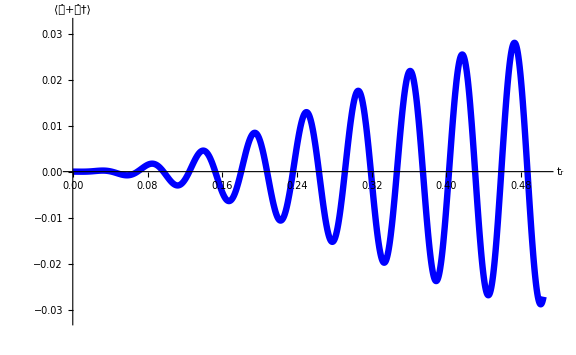

```mathematica
thick = 8 10^-3;
ElectricField[t_]:=Chop[(Ψ[t] )*.ElectricFieldMatrix.Ψ[t] ];
p1=Plot[{ElectricField[t]},{t,t0,tf+0.004},PlotRange->{-0.032,0.032},AxesOrigin->{0,0},AxesLabel->{Style[Subscript[t, r],30,Black],Style[Row@{AngleBracket["𝒶̂+𝒶̂†"]},30,Black]},AxesStyle->{{Black,FontSize->20},{Black,FontSize->20}},ImageSize->Large,PlotStyle->{{Solid,Blue,Thickness[thick]}}]
```

```mathematica
Clear@@DeleteCases[Names@"`*","p1"];
```

```mathematica
(* Change ϕ then run the appropriate code sections *)
```

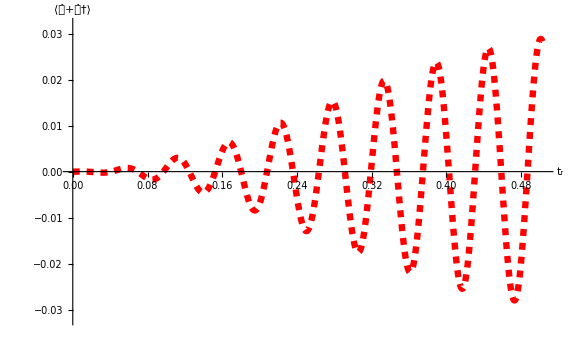

```mathematica
thick = 8 10^-3;
ElectricField[t_]:=Chop[(Ψ[t] )*.ElectricFieldMatrix.Ψ[t] ];
p2=Plot[{ElectricField[t]},{t,t0,tf+0.004},PlotRange->{-0.032,0.032},AxesOrigin->{0,0},AxesLabel->{Style[Subscript[t, r],30,Black],Style[Row@{AngleBracket["𝒶̂+𝒶̂†"]},30,Black]},AxesStyle->{{Black,FontSize->20},{Black,FontSize->20}},ImageSize->Large,PlotStyle->{{Dashed,Red,Thickness[thick]}}]
Show[p1,p2]
```

```mathematica
(*ωg1=0;
ωph=110;
Δ=10;
ωe1=ωg1+ωph+Δ;
υ=100;
ωe2=ωg1+Δ+υ;
ωg2=0;
IntPic=1;
Ω=1  ;
A= 1;*)
```

### Compiled Results

#### Heralding on Not G_2

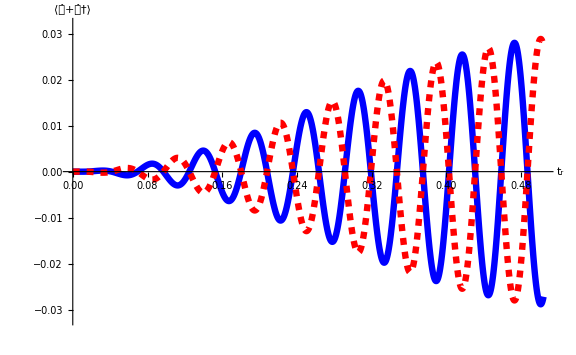

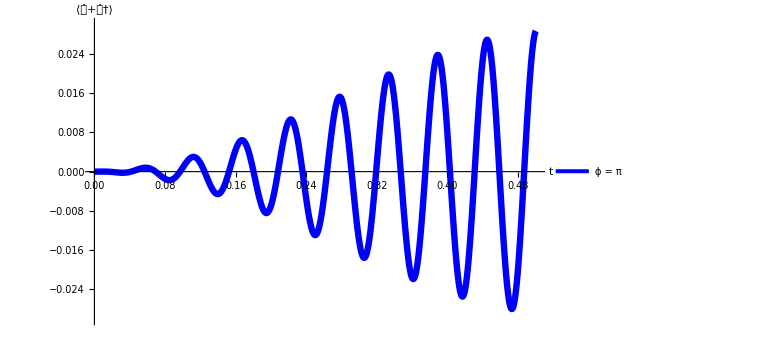

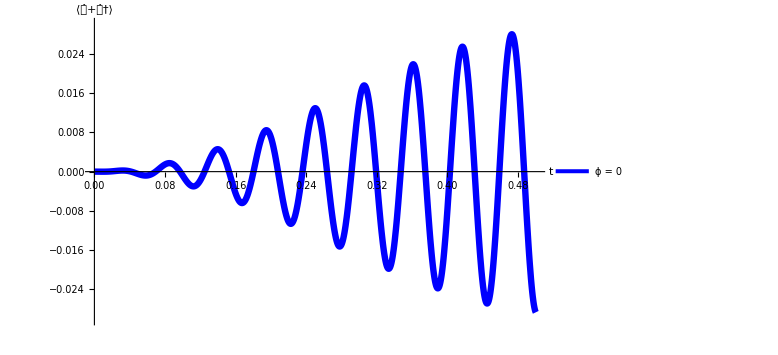

#### Heralding on Not G_1

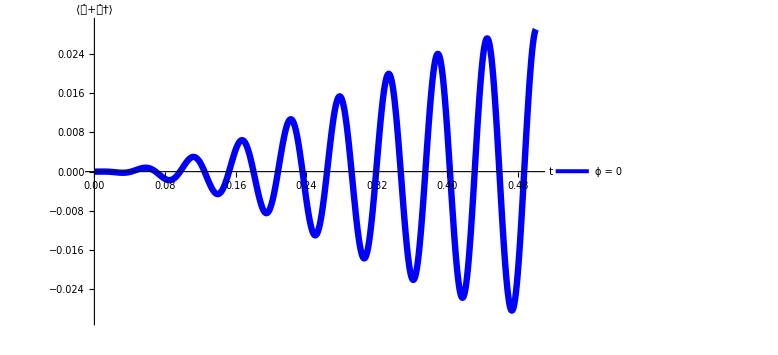

#### No Heralding